# Beugung

Dieses Mathematica-Notebook enthält ergänzende Abbildungen und Verdeutlichungen zum theoretischen Hintergrund des Beugungversuches bezüglich des Fortgeschrittenen Optik-Praktikums  (FP-I-O 2026)

## Fresnel-Beugung

Dieses Phänomen entsteht, wenn der Abstand zwischen Spalt und Schirm relativ klein ist. Die Breite des Spaltes wirkt sich auf den Verlauf der Wellen. Die genaue Form des eletrischen Feldes wird durch ein Fresnel-Integral gegeben. Dies gilt wenn die Fresnel-Zahl eine Ordnung 1 ist (definiert durch , λ die Wellenlänge, R der Abstand zwischen Spalt und Shirm, a typische Breite des Spaltes). In dieser Annäherung ist die Welle “sphärisch.” Für  gilt die gängigen Regeln der geometrischen Optik.  

Das elektrische Feld induziert ein elektisches Feld an entfernten Pünkten, gegeben durch
.
Der erste Ausdruck ist genau. Die obere Approximation ist in der Fresnel-Limus wahr.

```mathematica
σx=100;σy=100;
EGaussian[x_,y_,z_]:=Exp[-(x)^2/(2σx)]*Exp[-(y)^2/(2σy)] (*Gaussian electric field *)
EUniform[x_,y_,z_]:=1
ESquare[x_,y_,z_]:=Boole[Abs[x]<=σx/2&&Abs[y]<=σy/2]
E1DSquare[x_,y_,z_]:=Boole[Abs[x]<=σx/2]
Plot3D[ESquare[x,y,0],{x,-1,1},{y,-1,1},AxesStyle->Thick,TicksStyle->Directive["Label", 14],PlotStyle->Directive[Thick,Gray],MeshStyle->None,Lighting->"Accent",PlotLabel->"Spaltverlauf (z=0)",LabelStyle->{GrayLevel[0],14},Ticks->{{-1,0,1},{-1,0,1}},AxesLabel->{HoldForm["x"],HoldForm["y"]},Boxed->False]
```

-Graphics3D-

```mathematica
h[x_,y_,z_,λ_]:=Exp[ⅈ 2Pi/λ Sqrt[x^2+y^2+z^2]]/Sqrt[x^2+y^2+z^2] * z/Sqrt[x^2+y^2+z^2]*(1+ⅈ λ/(2Pi Sqrt[x^2+y^2+z^2])) (*Exact kernel*)
hFresnel[x_,y_,z_,λ_]:=Exp[ⅈ z 2Pi/λ ]/(ⅈ λ z)*Exp[ⅈ 2Pi/λ Sqrt[(x)^2+(y)^2]/(2z)] (*Fresnel approximation kernel*)
hComplex[z_,zz_,λ_]:=Exp[ⅈ 2Pi/λ Sqrt[Norm[z]^2+zz^2]]/Sqrt[Norm[z]^2+z^2] * z/Sqrt[Norm[z]^2+zz^2]*(1+ⅈ λ/(2Pi Sqrt[Norm[z]^2+zz^2])) (*Exact kernel*)
hFresnelComplex[z_,zz_,λ_]:=Exp[ⅈ zz 2Pi/λ ]/(ⅈ λ zz)*Exp[ⅈ 2Pi/λ Norm[z]/(2zz)] (*Fresnel approximation kernel*)
Manipulate[Plot3D[Re@hFresnel[x,y,z,λ],{x,-100,100},{y,-100,100},AxesStyle->Thick,TicksStyle->Directive["Label", 14],PlotStyle->Directive[Thick,Gray],MeshStyle->None,Lighting->Automatic,PlotLabel->"Fresnel-Kern (z=0)",LabelStyle->{GrayLevel[0],14},Ticks->{{-100,0,100},{-100,0,100},Automatic},AxesLabel->{HoldForm["x"],HoldForm["y"]},Boxed->False],{{z,10^-5},0,1},{{λ,10^-9},10^-12,10^2}]
Manipulate[ComplexPlot3D[hFresnelComplex[z,zz,λ],{z,-(100+100ⅈ),(100+100ⅈ)},PlotLegends->Automatic,AxesStyle->Thick,TicksStyle->Directive["Label", 14],PlotStyle->Directive[Thick,Gray],MeshStyle->None,Lighting->Automatic,PlotLabel->"Fresnel-Kern (z=0)",LabelStyle->{GrayLevel[0],14},Ticks->{{-100,0,100},{-100,0,100},Automatic},AxesLabel->{HoldForm["x"],HoldForm["y"]},Boxed->False],{{zz,0.1},0,1},{{λ,200},10^-12,10^3}]
```

```mathematica
ReIntegrand[x_,y_]:=Im[ESquare[xx,yy,0]*hFresnel[x-xx,y-yy,10000,1]]
NIntegrate[ReIntegrand[x,y],{xx,-50,50},{yy,-50,50},Method->"Oscillatory",MaxRecursion->100,AccuracyGoal->10,PrecisionGoal->10 ]
(*Mathematica is deciding that this is always zero??? WHY???*)
ReIntegrand[x,y]
```

NIntegrate::inumr: The integrand -Re[ⅇ^((ⅈ π √(Power[«2»]+Power[«2»]))/10000) Boole[Abs[xx]≤50&&Abs[yy]≤50]]/10000 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-50,50},{-50,50}}.

NIntegrate[ReIntegrand[x,y],{xx,-50,50},{yy,-50,50},Method→Oscillatory,MaxRecursion→100,AccuracyGoal→10,PrecisionGoal→10]

-Re[ⅇ^((ⅈ π √((x-xx)^2+(y-yy)^2))/10000) Boole[Abs[xx]≤50&&Abs[yy]≤50]]/10000

## Fraunhofer-Beugung (Einzelspalt)

Dieses Phenomäne entsteht, wenn der Abstand zwischen Spalt und Schirm groß im Vergleich zu Spaltbreite ist. Der Gangunterschied der Wellen verursacht unterschiedliche Interferenzen wegen Phasendifferenzen der emmiterten Elementarwellen. Die Bedingung der Intensitätsminima lässt sich durch geometrische Betrachtungen  ergeben:

```mathematica
parameters = {λ->700*10^-9,b->10^-5,c->100}
Intensity[θ_]:=c(Sin[Pi b/λ Sin[θ]]/(Pi b/λ Sin[θ]))^2
```

{λ→7/10000000,16→1/100000,1→100}

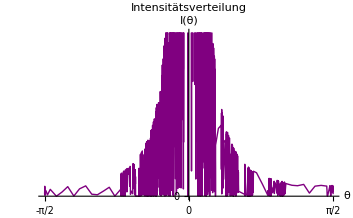

```mathematica
Plot[Intensity[θ]/.parameters,{θ,-Pi/2,Pi/2},AxesStyle->Thick,TicksStyle->Directive["Label", 14],PlotStyle->Directive[Thick,Purple],PlotLabel->"Intensitätsverteilung",LabelStyle->{GrayLevel[0],14},Ticks->{{-Pi/2,0,Pi/2},{0,0.5}},AxesLabel->{HoldForm["θ"],HoldForm["I(θ)"]}]
```

```mathematica
Manipulate[Plot[Evaluate[c(Sin[Pi b/λ Sin[θ]]/(Pi b/λ Sin[θ]))^2],{θ,-Pi/2,Pi/2},AxesStyle->Thick,TicksStyle->Directive["Label", 14],PlotStyle->Directive[Thick,Purple],PlotLabel->"Intensitätsverteilung",LabelStyle->{GrayLevel[0],14},AxesLabel->{HoldForm["θ"],HoldForm["I(θ)"]}] ,{λ,10^-12,10^1},{b,10^-12,10^1},{c,1,100}]
```

Die Lage der Intensitätsmaxima (bzw. -minima) kann aus der Funktion  bestimmt werden. Durch das Minimieren erhält man die Bedingung

```mathematica
FresnelMinima[θ_]:=D[Intensity[θ],θ]/.parameters
FresnelMinimaPoints = NSolve[FresnelMinima[θ]==0,θ,Reals(*,θ∈Interval[{-Pi/2,Pi/2}]*)]/.{C[1]->0} (*Set constant to zero, multiples of 2pi are all the same,filter out values with absolute value over pi/2*);
```

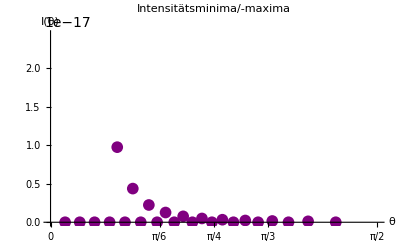

```mathematica
ListPlot[Thread[{θ/.FresnelMinimaPoints,Intensity[θ/.FresnelMinimaPoints]/.parameters}],PlotStyle->Directive[Purple,Large],AxesStyle->Thick,TicksStyle->Directive["Label", 14],LabelStyle->{GrayLevel[0],14},Ticks->{{0,Pi/6,Pi/4,Pi/3,Pi/2},Automatic},PlotRange->{{0,Pi/2},Automatic},AxesLabel->{HoldForm["θ"],HoldForm["I(θ)"]},PlotMarkers->{Automatic,12},PlotLabel->"Intensitätsminima/-maxima"] (**)
```

```mathematica
FresnelMinimaApproximation[θ_]=Normal[(Series[FresnelMinima[θ],{θ,0,1}]/.parameters)];
(*FresnelMinimaPoints = NSolve[FresnelMinima[θ]==0,θ,Reals(*,θ∈Interval[{-Pi/2,Pi/2}]*)]/.{C[1]->0} *)(*TO DO: replace theta with x/r, set equation fpor multiple integrers *)
nMax=10;
NSolve[FresnelMinimaApproximation[θ]==n π&&Element[n,Integers],θ];
FresnelMinimaPointsApproximation =(*θ/. *)NSolve[FresnelMinimaApproximation[θ]==n π&&Element[n,Integers],θ][[1,1]];
FresnelMinimaPointsApproximation = Table[
FresnelMinimaPointsApproximation/.n->i,
{i,-nMax,nMax}
](*Theta values*);
ListPlot[Thread[{(θ/. #)&/@FresnelMinimaPointsApproximation,Intensity[(θ/. #)&/@FresnelMinimaPointsApproximation]/.parameters}],PlotStyle->Directive[Purple,Large],AxesStyle->Thick,TicksStyle->Directive["Label", 14],LabelStyle->{GrayLevel[0],14},Ticks->{{0,Pi/4000},Automatic},PlotRange->{{0,Pi/4000},Automatic},AxesLabel->{HoldForm["θ"],HoldForm["I(θ)"]},PlotMarkers->{Automatic,12},PlotLabel->"Intensitätsminima/-maxima \n(Kleinwinkelentwickling)"]
```

$Aborted

$Aborted

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: {TerminatedEvaluation[RecursionLimit]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: {TerminatedEvaluation[RecursionLimit]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit::reclim will be suppressed during this calculation.

ReplaceAll::reps: {TerminatedEvaluation[RecursionLimit]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
SincFT[ω]:=FourierTransform[Intensity[θ],θ,ω]
Plot[SincFT[ω]/.parameters,{ω,-Pi/2,Pi/2},AxesStyle->Thick,AxesLabel->None,TicksStyle->Directive["Label", 14],PlotStyle->Directive[Thick,Dashed,Gray],PlotLabel->"Sinc Fourier-Transformierte",LabelStyle->{GrayLevel[0],14}] 
(*To do: labels at intervals of 2pi, sort out legends*)
```

-Graphics-

## Babinetsches Satz

## Fraunhofer-Beugung (Mehrfachspalt)

```mathematica
parametersN = Join[parameters,{s->1000/100000,n->2}](*s: Spaltabstand, n:  Anzahl der Spalte*);
IntensityN[θ_]=c(Sin[Pi b/λ Sin[θ]]/(Pi b/λ Sin[θ]))^2*(Sin[n Pi s/λ Sin[θ]]/Sin[(Pi s/λ Sin[θ])])^2/.parametersN ;
Manipulate[Plot[Evaluate[c(Sin[Pi b/λ Sin[θ]]/(Pi b/λ Sin[θ]))^2*(Sin[n Pi s/λ Sin[θ]]/Sin[(Pi s/λ Sin[θ])])^2],{θ,-Pi/10,Pi/10},Ticks->{{-Pi/10,0,Pi/10},Automatic},AxesStyle->Thick,TicksStyle->Directive["Label", 14],PlotStyle->Directive[Thick,Purple],PlotLabel->"Intensitätsverteilung \n (Mehrfachspalt)",LabelStyle->{GrayLevel[0],14},AxesLabel->{HoldForm["θ"],HoldForm["I(θ)"]}] ,{{λ,0.01},10^-12,10^1},{{b,0.1},10^-12,10^1},{{c,100},1,100},{{s,1},10^-9,10},{{n,2},1,10,1}]
Manipulate[Plot[Evaluate[c(Sin[Pi b/λ Sin[θ]]/(Pi b/λ Sin[θ]))^2*(Sin[n Pi s/λ Sin[θ]]/Sin[(Pi s/λ Sin[θ])])^2],{θ,-Pi/2,Pi/2},Ticks->{{-Pi/2,0,Pi/2},Automatic},AxesStyle->Thick,TicksStyle->Directive["Label", 14],PlotStyle->Directive[Thick,Purple],PlotLabel->"Intensitätsverteilung \n (Mehrfachspalt)",LabelStyle->{GrayLevel[0],14},AxesLabel->{HoldForm["θ"],HoldForm["I(θ)"]}] ,{{λ,0.01},10^-12,10^1},{{b,0.1},10^-12,10^1},{{c,100},1,100},{{s,1},10^-9,10},{{n,2},1,10,1}]
```

```mathematica
(*FresnelMinimaPointsN = DeleteDuplicates[Table[Quiet@Check[FindRoot[D[IntensityN[θ],θ]==0,{θ,guess}],Nothing],{guess,-Pi/2,Pi/2,0.0001}]];*)
(*FresnelMinimaPointsN = NSolve[IntensityN[θ]==0,θ,Reals]
ListPlot[Thread[{θ/.FresnelMinimaPointsN,IntensityN[θ/.FresnelMinimaPointsN]/.parameters}],PlotStyle->Directive[Purple,Large],AxesStyle->Thick,TicksStyle->Directive["Label", 14],LabelStyle->{GrayLevel[0],14},Ticks->{{-Pi/2,0,Pi/2},Automatic},PlotRange->{{-Pi/2,0,Pi/2},Automatic},AxesLabel->{HoldForm["θ"],HoldForm["I(θ;N)"]},PlotMarkers->{Automatic,4},PlotLabel->"Intensitätsminima/-maxima \n(Mehrfachspalt)"] *)
```

## Fresnel-Beugung an der Kante

Fällt Licht auf eine geradlinige Kante, wird es gebeugt. (Die analytische Form ergibt keine geschlossene Lösung der Intensitätsverteilung.)

```mathematica
(*Correct for standard mathematica normalization*)
U[w_]:=Sqrt[2/Pi]*FresnelS[w*Sqrt[2/Pi]];
V[w_]:=Sqrt[2/Pi]*FresnelC[w*Sqrt[2/Pi]];

(*Intensität parallel zur Halbebene*)
IntensityKante[w_]:=I0/2((U[w]^2+1/2)^2+(V[w]^2+1/2)^2);

(*Geometric parameters*)
parametersKante = {Dp->1,Dq->10,λ->0.01,I0->1}
parametersLength = {w->z/b,b->Sqrt[λ*Dp*(Dp+Dq)/(Pi*Dq)]}
variablesKante = { b->Sqrt[λ*Dp*(Dp+Dq)/(Pi*Dq)]}/.parametersLength/.parametersKante
U[(w/.variablesKante)]/.variablesKante
```

{Dp→1,Dq→10,λ→0.01,I0→1}

{w→z/b,b→(√((Dp (Dp+Dq) λ)/Dq))/(√π)}

{0.0591727→0.0591727}

√(2/π) FresnelS[√(2/π) w]

```mathematica
Manipulate[Plot[(I0/2((U[z/b]^2+1/2)^2+(V[z/b]^2+1/2)^2))/.parametersLength,{z,0,10},Ticks->{{-10,0,10},Automatic},AxesStyle->Thick,TicksStyle->Directive["Label", 14],PlotStyle->Directive[Thick,Purple],PlotLabel->"Intensitätsverteilung \n (Fresnel-Beugung an der Kante)",LabelStyle->{GrayLevel[0],14},AxesLabel->{HoldForm["w"],HoldForm["I(w)"]},PlotRange->{0,I0}] ,{{I0,1},1,100},{{b,1},10^-12,10^1}]
(*(I0/2((U[z/b]^2+1/2)^2+(V[z/b]^2+1/2)^2))/.parametersLength*)
```

ReplaceAll::reps: {parametersLength} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

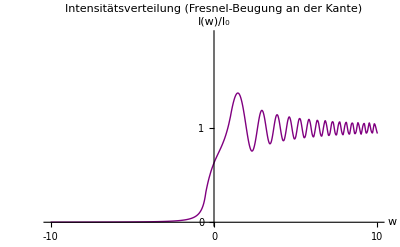

```mathematica
IntensityShaddow1[w_]:=I0(1+Sqrt[1/Pi]Sin[w^2-Pi/4]/w) (*w>1*)
IntensityShaddow2[w_]:=I0/(4Pi w^2) (*w<0 and |w|>>1*)
IntensityShaddow = Join[IntensityShaddow2@Range[-10,-0.5,0.1],IntensityShaddow1@Range[1,10,0.1]];
LengthValues = Join[Range[-10,-0.5,0.1],Range[1,10,0.1]];
IntensityShaddow = Transpose[{LengthValues, IntensityShaddow}];
Plot[Interpolation[IntensityShaddow/.I0->1][w],{w,-10,10},Ticks->{{-10,0,10},{0,1}},AxesStyle->Thick,TicksStyle->Directive["Label", 14],PlotStyle->Directive[Thick,Purple],PlotLabel->"Intensitätsverteilung \n (Fresnel-Beugung an der Kante)",LabelStyle->{GrayLevel[0],14},PlotRange->{0,2},AxesLabel->{HoldForm["w"],HoldForm["I(w)/I_0"]}]
(*TO DO: *)
```